```mathematica
sphere[x_]:=Module[
{},Sum[(x[[i]])^2,{i,Length@x}]]
```

```mathematica
DE[f_,dim_]:=Module[{},
G1=RandomReal[{-500,500},{20,dim}];
CR=0.8;
F=0.5;
solution={};
G={};

For[k=1,k<=100,k++,
AppendTo[solution,Min@Table[f[G1[[i]]],{i,20}]];
AppendTo[G,G1];
(*Mutation*)

GRest=Table[Complement[G1,{G1[[i]]}],{i,20}];
Table[Length@GRest[[i]],{i,20}];
R2=Table[RandomChoice[GRest[[i]]],{i,20}];
R1=G1;
GRest2=Table[Complement[G1,{R1[[i]]},{R2[[i]]}],{i,20}];
R3=Table[RandomChoice[GRest2[[i]]],{i,20}];
GRest3=Table[Complement[G1,{R1[[i]]},{R2[[i]]},{R3[[i]]}],{i,20}];
R4=Table[RandomChoice[GRest3[[i]]],{i,20}];
MutantVector=Table[R2[[i]]+F*(R3[[i]]-R4[[i]]),{i,20}];
(*Crossover*)
child=Table[Table[0,dim],20];
For[i=1,i<=20,i++,
jrand =RandomInteger[{1,dim}];
For[j=1,j<=dim,j++,If[RandomReal[{0,1}]<=CR||j==jrand,child[[i]][[j]]=MutantVector[[i]][[j]],child[[i]][[j]]=R1[[i]][[j]]]]];
For[i=1,i<=20,i++,If[f[child[[i]]]<f[R1[[i]]],G1[[i]]=child[[i]]]];


];
Return@solution
]
```

```mathematica
DE[sphere,10]
```

{417917.,417917.,417917.,417917.,417917.,417917.,355575.,355575.,310515.,222071.,222071.,222071.,222071.,222071.,181654.,151698.,151698.,151698.,44367.4,44367.4,44367.4,44367.4,44367.4,44367.4,44367.4,44367.4,44367.4,44367.4,41673.2,38212.4,38212.4,29376.4,27460.2,27047.,26141.3,26141.3,22109.8,22109.8,14050.5,14050.5,14050.5,13378.5,13378.5,13378.5,13378.5,13378.5,10835.8,10835.8,9284.89,7991.63,7939.26,7649.07,5378.71,5177.02,3359.73,3359.73,3359.73,2145.88,2145.88,2145.88,2145.88,2145.88,1817.12,1817.12,1227.82,1227.82,1021.56,1021.56,1021.56,1021.56,1021.56,946.516,660.784,591.584,591.584,591.584,591.584,591.584,407.452,407.452,407.452,407.452,376.509,374.698,367.706,189.994,189.994,189.994,189.994,189.994,140.192,140.192,138.012,104.573,104.573,104.573,104.573,89.633,86.905,73.8687}

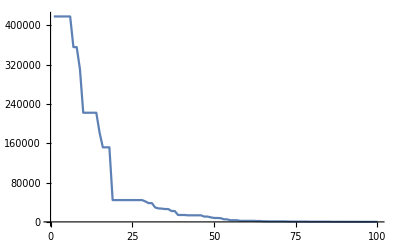

```mathematica
ListLinePlot@solution
```

```mathematica
(*SUM OF DIFFERENT POWERS FUNCTION*)
```

```mathematica
SDP[x_]:=Module[{l=Length@x},Sum[Abs[x[[i]]]^(i+1),{i,l}]]
```

```mathematica
(*SUM SQUARES FUNCTION*)
```

```mathematica
SS[x_]:=Module[{l=Length@x},Sum[i*(x[[i]]^2),{i,l}]]
```

```mathematica
(*TRID FUNCTION*)
```

```mathematica
Trid[x_]:=Module[{l=Length@x},Sum[(x[[i]]-1)^2,{i,l}]-Sum[x[[i]]*x[[i-1]],{i,2,l}]]
```

```mathematica
(*ROTATED HYPER-ELLIPSOID FUNCTION*)
```

```mathematica
RHE[x_]:=Module[{l=Length@x},Sum[Sum[x[[j]]^2,{j,i}],{i,l}]]
```

```mathematica
DE[SDP,10]
ListLinePlot@solution
```

{7.11956×10^19,7.11956×10^19,7.11956×10^19,7.11956×10^19,6.93368×10^17,6.93368×10^17,6.93368×10^17,6.93368×10^17,6.93368×10^17,6.93368×10^17,6.93368×10^17,6.93368×10^17,6.93368×10^17,6.93368×10^17,4.94192×10^16,4.94192×10^16,4.94192×10^16,7.48654×10^15,7.48654×10^15,7.37136×10^14,7.37136×10^14,7.37136×10^14,7.37136×10^14,7.37136×10^14,1.08918×10^14,1.08918×10^14,1.08918×10^14,1.08918×10^14,6.66636×10^13,9.21422×10^12,9.21422×10^12,9.21422×10^12,9.21422×10^12,7.91165×10^11,7.91165×10^11,6.24499×10^11,5.00533×10^11,5.00533×10^11,5.00533×10^11,5.00533×10^11,3.30024×10^11,2.1379×10^11,2.08614×10^11,1.23805×10^11,8.68724×10^10,7.38192×10^10,1.33017×10^10,1.33017×10^10,1.33017×10^10,1.33017×10^10,1.33017×10^10,6.5629×10^9,6.5629×10^9,6.5629×10^9,6.41809×10^9,6.41809×10^9,4.50562×10^9,9.36836×10^8,9.36836×10^8,9.02175×10^8,9.02175×10^8,3.27316×10^8,2.29242×10^8,2.29242×10^8,2.29242×10^8,3.89703×10^7,2.27895×10^7,2.27895×10^7,2.27895×10^7,2.27895×10^7,3.72452×10^6,3.72452×10^6,3.72452×10^6,3.72452×10^6,3.72452×10^6,3.72452×10^6,3.72452×10^6,2.65996×10^6,2.32804×10^6,1.82408×10^6,1.82408×10^6,962656.,570132.,570132.,218849.,140960.,140960.,140960.,140960.,136234.,24261.2,24261.2,24261.2,6841.68,2550.27,2550.27,2550.27,2550.27,1834.1,1834.1}

-Graphics-

{622453.,622453.,622453.,622453.,615474.,347032.,347032.,249692.,249692.,249692.,249692.,249692.,249692.,161074.,161074.,161074.,161074.,111338.,111338.,111338.,89329.9,89329.9,46325.,46325.,46325.,46325.,43838.,23518.9,23518.9,23518.9,23518.9,23518.9,23518.9,23518.9,22295.9,22295.9,19597.8,11801.6,11801.6,8593.78,8593.78,8593.78,4903.85,4903.85,4903.85,4448.36,4448.36,4448.36,4448.36,4058.11,3758.38,3758.38,994.791,994.791,994.791,968.509,968.509,622.8,622.8,622.8,517.388,463.002,463.002,463.002,374.684,374.684,374.684,374.684,244.752,232.512,232.512,232.512,150.531,125.759,125.759,125.759,125.759,125.759,125.759,109.782,84.6402,84.6402,84.6402,84.6402,84.6402,55.3552,55.3124,52.443,52.443,34.27,34.27,24.8323,24.8323,24.8323,24.8323,23.1928,20.8648,18.401,18.401,18.401}

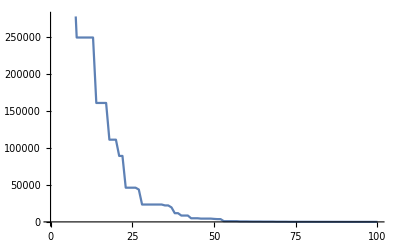

```mathematica
DE[SS,10]
ListLinePlot@solution
```

{243634.,243634.,243634.,243634.,243634.,243634.,243634.,243634.,124522.,124522.,124522.,123816.,123816.,110278.,110278.,70709.,70709.,70709.,70709.,70709.,70709.,70709.,62537.3,62537.3,61205.4,60850.7,60850.7,57074.5,57074.5,48199.,40898.4,34630.1,26416.5,26416.5,26416.5,23020.4,23020.4,23020.4,23020.4,18855.8,18855.8,17203.4,17203.4,15069.6,11453.,11453.,11078.9,8771.14,7908.28,7908.28,6561.62,6561.62,4877.32,4579.74,4579.74,4579.74,4579.74,4579.74,4579.74,3258.28,3258.28,3258.28,3258.28,2513.35,2513.35,2513.35,1719.95,1719.95,1719.95,1719.95,1719.95,1719.95,1719.95,1719.95,1719.95,1608.02,1608.02,1565.39,1565.39,1519.8,1348.54,1348.54,1348.54,1348.54,1348.54,1348.54,1348.54,1348.54,1348.54,1205.87,1205.87,1163.12,1037.6,1037.6,1037.6,1037.6,1003.39,938.245,926.574,926.574}

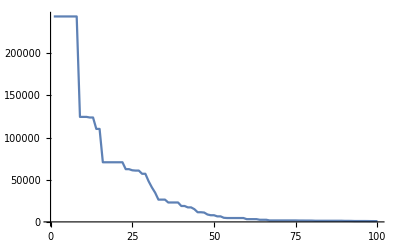

```mathematica
DE[Trid,10]
ListLinePlot@solution
```

{1.10288×10^6,1.10288×10^6,1.10288×10^6,1.10288×10^6,1.10288×10^6,1.10288×10^6,1.10288×10^6,1.10288×10^6,884735.,654125.,654125.,654125.,654125.,521728.,521728.,426873.,388468.,388468.,388468.,231708.,231708.,231708.,231708.,185339.,185339.,185339.,144916.,88374.9,88374.9,53332.9,53332.9,53332.9,53332.9,49695.1,49695.1,49695.1,42178.3,24916.4,22327.2,18202.1,18202.1,18202.1,13518.6,13518.6,13518.6,9368.15,8772.6,8374.52,8051.8,3829.97,3586.81,2903.68,2903.68,2903.68,2903.68,2419.69,2419.69,1897.4,1526.69,1526.69,1226.72,1226.72,1226.72,1226.72,1226.72,1226.72,985.251,837.769,837.769,837.769,837.769,691.732,633.795,633.795,606.294,299.914,299.914,299.914,299.914,299.914,200.249,200.249,161.257,161.257,145.313,145.313,145.313,72.0935,72.0935,67.4188,67.4188,48.726,48.726,48.726,48.726,48.726,35.6694,35.6694,35.6694,35.6694}

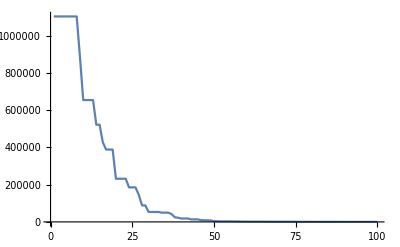

```mathematica
DE[RHE,10]
ListLinePlot@solution
```